# QMRITools Demonstration

In this demo notebook some functionality of the QMRI toolbox is demonstrated.

Initialization

Load the toolbox and specify the directory of the demo data

```mathematica
<<QMRITools`
```

```mathematica
SetDirectory["D:\\Werk\\Workspace\\QMRITools\\testdata"];
```

### List all Packages and toolboxes

List of all the QMRITool packages and functions that are loaded

```mathematica
QMRIToolsPackages[]
```

{CardiacTools,CoilTools,DenoiseTools,DixonTools,ElastixTools,GeneralTools,GradientTools,ImportTools,IVIMTools,JcouplingTools,MaskingTools,NiftiTools,PhysiologyTools,PlottingTools,ProcessingTools,RelaxometryTools,SimulationTools,TensorTools,VisteTools}

```mathematica
QMRIToolsFunctions[25]
```

Functions

ADCCalc | ClearTemporaryVariables | DeNoise | ExportNii | GetSliceNormal | ImportNiiT1 | MaskHelix | PlotCorrection | ReadDicom | SequenceSpinEcho | StdFilter
AddNoise | CoilSNRCalc | Deriv | ExportVol | GetSliceNormalDir | ImportNiiT2 | MeanNoZero | PlotData | ReadDicomDiff | SequenceSteam | StichData
AlignRespLog | ColorFAPlot | DevideNoZero | ExtractNiiFiles | GetSlicePositions | ImportPhyslog | MeanRange | PlotData3D | ReadDicomDir | SequenceTSE | SumOfSquares
AngleCalc | CompilebleFunctions | DictionaryMinSearch | FACalc | GetSpinSystem | ImportRespirect | MeanSignal | PlotDefGrid | ReadDicomDirDiff | SetupDataStructure | SysTable
AngleMap | CompressNiiFiles | DixonReconstruct | FConvert | GfactorSimulation | ImportVol | MeanStd | PlotDuty | ReadGradients | ShiftPar | T1Fit
AnisoFilterTensor | ConcatenateDiffusionData | DixonToPercent | FConverti | GradBmatrix | InvertDataset | MedCouple | PlotIVIM | ReadTransformParameters | SigmaCalc | T1rhoFit
ApplyCrop | ConditionNumberCalc | DriftCorrect | FiberDensityMap | GradientPlot | IVIMCalc | MedianNoZero | PlotMoments | ReadVoxSize | Signal | T2Fit
AutoCropData | ConvertGrads | DTItoolExp | FiberLengths | GradRead | IVIMCorrectData | MemoryUsage | PlotPhyslog | RegisterCardiacData | SimAddPhase | TensMat
BayesianIVIMFit2 | Correct | DTItoolExpFile | FileSelect | GradSeq | IVIMFunction | MergeSegmentations | PlotRespiract | RegisterData | SimAngleParameters | Tensor
BayesianIVIMFit3 | CorrectBmatrix | DTItoolExpInd | FinalGrads | GridData | IVIMResiduals | NNLeastSquares | PlotSegmentMask | RegisterDataSplit | SimEvolve | TensorCalc
BlochSeries | CorrectGradients | DTItoolExpTens | FindCoilPosition | HelixAngleCalc | JoinSets | NoiseCorrelation | PlotSegments | RegisterDataTransform | SimHamiltonian | TensorCorrect
Bmatrix | CorrectJoinSetMotion | ECalc | FindCrop | Hist | LapFilter | NoiseCovariance | PlotSequence | RegisterDataTransformSplit | SimParameters | TensVec
BmatrixCalc | CorrectParMap | ECVCalc | FindMaxDimensions | Hist2 | ListSpherePlot | NonLinearEPGFit | PlotSimulation | RegisterDiffusionData | SimReadout | ThetaConv
BmatrixConv | CreateDiffData | EigensysCalc | FindOrder | HistogramPar | LoadCoilSetup | NormalizeData | PlotSimulationAngle | RegisterDiffusionDataSplit | SimRotate | ThetaConvi
BmatrixInv | CreateT2Dictionary | EigenvalCalc | FindOutliers | HomoginizeData | LoadCoilTarget | NumberTableForm | PlotSimulationAngleHist | RemoveIsoImages | SimSignal | TransData
BmatrixRot | CropData | EigenvecCalc | FitData | ImportBmat | LoadFiberTracts | OverPlusCalc | PlotSimulationHist | RemoveMaskOverlaps | SimSpoil | TransformData
BmatrixToggle | CutData | EnergyCalc | FracCorrect | ImportBval | LogNoZero | PadToDimensions | PlotSimulationVec | RescaleData | SimulateSliceEPG | TransmuralPlot
BullseyePlot | Data2DToVector | EPGSignal | FullGrad | ImportBvalvec | MADNoZero | ParameterCalc | PlotSpectrum | RescaleSegmentation | SmartMask | TriExponentialT2Fit
BvalRead | Data3DToVector | EPGT2Fit | GenerateGradients | ImportBvec | MakeCoilLayout | ParameterFit | Pulses | ResidualCalc | SmoothMask | UniqueBvalPosition
CalculateGfactor | DataTranformation | ErrorPlot | GenerateGradientsGUI | ImportDTI | MakeECVBloodMask | ParameterFit2 | QMRIToolsFuncPrint | ReverseCrop | SmoothSegmentation | Unwrap
CalculateMoments | DatRead | ExcludeSlices | GetGradientScanOrder | ImportExploreDTItens | MakeNoisePlots | PCADeNoise | QMRIToolsFunctions | RMSNoZero | SNRCalc | UnwrapSplit
CalculateWallMap | DatTot | ExpNoZero | GetMaskData | ImportGradObj | MakeSliceImages | PCAFitEq | QMRIToolsPackages | ROIMask | SNRMapCalc | VectorToData
CalibrateEPGT2Fit | DatTotXLS | ExportBmat | GetMaskMeans | ImportNii | MakeWeightMask | PCAFitHist | RadialSample | SaveImage | SortDiffusionData | WeightMapCalc
CardiacSegment | DatWrite | ExportBval | GetPulseProfile | ImportNiiDiff | Mask | PhaseAlign | ReadBrukerDiff | SegmentMask | SplitSegmentations | 
CentralAxes | DcmToNii | ExportBvec | GetSliceData | ImportNiiDix | MaskData | PlotContour | ReadBvalue | SequencePulseAcquire | SplitSets |

Options

AffineDirections | ConvertDcm | DropSamples | GetMaskOutput | IVIMTensFit | MethodReg | OutputCoilSurface | PlotRange | RobustFitParameters | Steps
AnisoFilterSteps | CorrectPar | DropSlices | GOutput | JoinSetSplit | MethodReg | OutputImage | PlotRange | RotateGradient | StepSizeI
AnisoKappa | CropInit | EPGCalibrate | GradType | LineStep | MethodRegA | OutputMethod | PlotRange | RotateGradients | Strictness
AnisoStepTime | CropOutput | EPGFitPoints | GRegularization | LineThreshold | MonitorCalc | OutputPlot | PlotRange | RotationCorrect | SwitchAxes
AnisoWeightType | CropPadding | EPGMethod | GridLineSpacing | Linewidth | MonitorEPGFit | OutputSamples | PlotRange | RowSize | TableAlignments
AxesLabel | CutOffMethod | EPGRelaxPars | HelixMethod | LinewidthShape | MonitorIVIMCalc | OutputSNR | PlotSolution | Runs | TableDepth
AxesMethod | DeleteTempDirectory | EPGSmoothB1 | HistogramBins | MagnetizationVector | MonitorUnwrap | OutputTransformation | PlotSpace | SampleStep | TableDirections
BackgroundValue | DeNoiseIterations | FieldStrength | HistogramBinsA | MakeCheckPlot | MotionCorrectSets | OutputType | PlotStyle | ScaleCorrect | TableHeadings
BinaryType | DeNoiseKernel | FileType | ImageLegend | MaskClosing | NiiDataType | OutputWeights | PositiveZ | Scaling | TableMethod
BloodMaskRange | DeNoiseMonitor | FilterMaps | ImageResolution | MaskCompartment | NiiMethod | PadDirection | PrintTempDirectory | SeedDensity | TableSpacing
BmatrixOut | DictB1Range | FilterShape | ImageSize | MaskComponents | NiiScaling | PaddOverlap | RadialSamples | ShowFit | TempDirectory
BsplineDirections | DictT2fRange | FilterSize | ImageSize | MaskFiltKernel | NoiseSize | PadValue | ReadoutBandwith | ShowHelixPlot | TensOutput
BsplineSpacing | DictT2Range | FilterType | ImageSize | MaskSmoothing | NormalizeIVIM | Parallelize | ReadoutOutput | SliceRange | TextOffset
BullPlotMethod | DistanceMeasure | FindTransform | ImageSize | MaskWallMap | NormalizeSets | Parallelize | ReadoutPhase | SliceRangeSamples | TextSize
CenterFrequency | Distribution | FitConstrains | ImageSize | MeanMethod | NormalizeSignal | PCAComponents | ReadoutSamples | SmartMaskOutput | UnitMulti
ChainSteps | DixonAmplitudes | FitFunction | InterpolationOrder | MeanRes | NumberSamples | PCAFitParameters | RegistrationTarget | SmartMethod | UnwrapDimension
CoilArrayPlot | DixonFieldStrength | FitOutput | InterpolationOrder | Method | NumberSamplesA | PCAKernel | Reject | SmoothHelix | UpdateStep
CoilSurfaceVoxelSize | DixonFilterInput | FitSigma | InterpolationOrderReg | Method | OrderSpan | PCAOutput | Reject | SmoothSNR | UseGPU
ColorFunction | DixonFilterOutput | FixPseudoDiff | InterpolationOrderRegA | Method | OutlierIncludeZero | PCATollerance | RejectMap | SortVecs | UseGrad
ColorFunction | DixonFilterSize | FixPseudoDiffSD | Iterations | Method | OutlierIterations | PCAWeighting | ReportFits | SpectrumColor | UseMask
ColorFunction | DixonFrequencies | FlipAxes | IterationsA | Method | OutlierMethod | PeakNumber | Resolutions | SphereColor | UseMask
ColorValue | DixonIterations | FlipBvec | IVIMComponents | Method | OutlierOutput | PhaseEncoding | ResolutionsA | SphereSize | VisualOpt
CompressNii | DixonMaskThreshhold | FlipGrad | IVIMConstrained | Method | OutlierRange | PlotColor | ReverseData | SplitMethod | WindowTitle
ConditionCalc | DixonPrecessions | FullOutput | IVIMConstrains | Method | OutputCalibration | PlotLabel | ReverseSets | StartPoints | 
ContourStyle | DixonTollerance | FullSphere | IVIMFixed | Method | OutputCheckImage | PlotLabel | RobustFit | StartSlices |

```mathematica
CompilebleFunctions[]
```

Abs | Decrement | Last | Quotient | TimesBy
AddTo | Delete | Length | Ramp | Tr
And | DeleteCases | Less | Random | Transpose
Append | Dimensions | LessEqual | RandomChoice | Unequal
AppendTo | Divide | List | RandomComplex | Union
Apply | DivideBy | Log | RandomInteger | Unitize
ArcCos | Do | Log10 | RandomReal | UnitStep
ArcCosh | Dot | Internal`Log1p | RandomSample | UnsameQ
ArcCot | Drop | Log2 | RandomVariate | VectorQ
ArcCoth | Equal | LogGamma | Range | Which
ArcCsc | Erf | LogisticSigmoid | Re | While
ArcCsch | Erfc | LucasL | RealAbs | With
ArcSec | EvenQ | Map | RealSign | Xor
ArcSech | Exp | MapAll | Internal`ReciprocalSqrt | 
ArcSin | Internal`Expm1 | MapAt | ReplacePart | 
ArcSinh | Fibonacci | MapIndexed | Rest | 
ArcTan | First | MapThread | Return | 
ArcTanh | FixedPoint | NDSolve`FEM`MapThreadDot | Reverse | 
Arg | FixedPointList | MatrixQ | RotateLeft | 
Array | Flatten | Max | RotateRight | 
ArrayDepth | NDSolve`FEM`FlattenAll | MemberQ | Round | 
Internal`Bag | Floor | Min | RuleCondition | 
Internal`BagPart | Fold | Minus | SameQ | 
BitAnd | FoldList | Mod | Scan | 
BitNot | For | Compile`Mod1 | Sec | 
BitOr | FractionalPart | Module | Sech | 
BitXor | FreeQ | Most | SeedRandom | 
Block | Gamma | N | Select | 
BlockRandom | Compile`GetElement | Negative | Set | 
Boole | Goto | Nest | SetDelayed | 
Break | Greater | NestList | Compile`SetIterate | 
Cases | GreaterEqual | NonNegative | Sign | 
Catch | Gudermannian | Not | Sin | 
Ceiling | Haversine | OddQ | Sinc | 
Chop | If | Or | Sinh | 
Internal`CompileError | Im | OrderedQ | Sort | 
System`Private`CompileSymbol | Implies | Out | Sqrt | 
Complement | Increment | Outer | Internal`Square | 
ComposeList | Indexed | Part | Internal`StuffBag | 
CompoundExpression | Inequality | Partition | Subtract | 
Conjugate | Compile`InnerDo | Piecewise | SubtractFrom | 
ConjugateTranspose | Insert | Plus | Sum | 
Continue | IntegerDigits | Position | Switch | 
Cos | IntegerPart | Positive | Table | 
Cosh | Intersection | Power | Take | 
Cot | InverseGudermannian | PreDecrement | Tan | 
Coth | InverseHaversine | PreIncrement | Tanh | 
Count | Compile`IteratorCount | Prepend | TensorRank | 
Csc | Join | PrependTo | Throw | 
Csch | Label | Product | Times |

### Memory Usage

```mathematica
MemoryUsage[]
```

MemoryUsage gives a visual overview of all datasets

Basic Data manipulation and visualisation

### Import and show Data

```mathematica
(*simple 3D dataset*)
{data,vox}=ImportNii["twoLegs.nii"];
```

```mathematica
(*plot the data*)
PlotData[data,vox]
```

```mathematica
(*plot the data as a grid*)
PlotData[GridData[data[[1;;;;3]],3]]
```

### Automatically find cross section images

By also providing the voxel size the pos is in mm else it will be in vox position

```mathematica
pos=GetSlicePositions[data,MakeCheckPlot->True];
pdat=GetSliceData[data,pos];
```

```mathematica
Grid[MakeSliceImages[pdat,vox,ColorFunction->"GrayTones"]]
```

```mathematica
Grid[MakeSliceImages[pdat,vox,ColorFunction->"DarkRainbow",ImageLegend->True]]
```

### Rescaling Data

```mathematica
(*to specific dimensions*)
dataReD=RescaleData[data,{50,100,100}];

Dimensions[data]
Dimensions[dataReD]
```

{25,160,160}

{50,100,100}

```mathematica
(*to specific voxel Size*)
voxNew={4,2,2};
dataRe=RescaleData[data,{vox,voxNew}];

Dimensions[data]
Dimensions[dataRe]
```

{25,160,160}

{38,240,240}

### Cropping

#### Automatic crop

```mathematica
crop=FindCrop[data];
```

```mathematica
dataCrop=ApplyCrop[data,crop];
```

```mathematica
PlotData[dataCrop,vox]
```

#### Apply To Rescaled Data

```mathematica
dataCR=ApplyCrop[dataRe,crop,{vox,voxNew}];
```

```mathematica
PlotData[dataCR]
```

#### Manual crop

```mathematica
{dataCrop,crop}=CropData[data,vox];
Dimensions[dataCrop]
```

{25,85,122}

```mathematica
PlotData[dataCrop,vox]
```

```mathematica
(*reverse the crop to the original dimensions*)
dim=Dimensions[data]
dataRev=ReverseCrop[dataCrop,dim,crop];
Dimensions[dataRev]
dataRev==data
```

{25,160,160}

True

### Splitting Data

#### Split and Stitch

```mathematica
{left,right,cut}=CutData[data];
```

-Graphics-

```mathematica
PlotData[left,right,vox]
```

```mathematica
dataStich=StichData[left,right];
```

```mathematica
PlotData[dataStich]
```

```mathematica
(*cut with known value*)
{left,right,cut}=CutData[data,80];
```

#### Example make both legs left

```mathematica
(*Split in Left and right leg*)
{left,right,cut}=CutData[data];
(*crop to minimal Space and flip right leg*)
{leftC,rightC}=AutoCropData[#][[1]]&/@{left,right};
rightC=Reverse[rightC,{3}];
dataC={leftC,rightC};
(*find maximal common dimensions and make into one dataset of same dimensions*)
dimMax=FindMaxDimensions[dataC];
dataP=Transpose[PadToDimensions[#,dimMax]&/@dataC];
```

```mathematica
PlotData[dataP,vox]
```

Masking

### Import Data

```mathematica
(*simple 3D dataset with segmentations*)
{data,vox}=ImportNii["twoLegs.nii"];
{labels,vox}=ImportNii["labels.nii"];
```

```mathematica
PlotData[data,labels]
```

### Create Mask

#### Automated and threshold masking

```mathematica
mask=Mask[data];
```

```mathematica
PlotData[data,mask]
```

Create mask based on threshold, smooth the mask, close holes larger then two, maintain two separate masks.
Default the algorithm finds only one mask but it is possible to maintain two separate masks.

```mathematica
cleanMask1=Mask[data,15,MaskSmoothing->True,MaskClosing->2];
```

```mathematica
cleanMask2=Mask[data,15,MaskSmoothing->True,MaskClosing->2,MaskComponents->2];
```

```mathematica
PlotData[data,Transpose@{cleanMask1,cleanMask2},vox]
```

Apply the mask

```mathematica
dataMask=MaskData[data,cleanMask2];
```

```mathematica
PlotData[data,dataMask]
```

#### Manual segmentation processing

Separate a segmentation with multiple labels into individual masks.

```mathematica
{seg,lab}=SplitSegmentations[labels];
lab (*the label numbers*)
Dimensions[labels]
Dimensions[seg]
```

{13,14,15,16,17,18,19,20,21,22,23,24,25,26}

{25,160,160}

{25,14,160,160}

Smooth the segmentations labels should be separate volumes and can be joined after smoothing

```mathematica
segS=SmoothSegmentation[seg];
labelsS=MergeSegmentations[segS,lab];
```

```mathematica
PlotData[labels,labelsS,vox]
```

Split a Segmentation in 5 equal parts along the slice direction

```mathematica
segSplit=SegmentMask[segS[[All,5]],5];
Dimensions[segSplit]
```

{5,25,160,160}

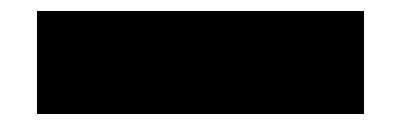
-Graphics--Graphics-

```mathematica
segPlot=MergeSegmentations[Transpose@segSplit,{1,2,3,4,5}];
Row@Flatten@MakeSliceImages[GetSliceData[segPlot,{{},{90},{57}}],vox,ColorFunction->"DarkRainbow",ImageLegend->True]
```

### Rescaling Segmentations

```mathematica
Dimensions[labels]
labelsRescale=RescaleSegmentation[labels,{50,100,100}];
Dimensions[labelsRescale]
```

{25,160,160}

{50,100,100}

```mathematica
mask=Mask[data];
Dimensions[mask]
maskRescale=RescaleSegmentation[mask,{50,100,100}];
Dimensions[maskRescale]
```

{25,160,160}

{50,100,100}

```mathematica
PlotData[labelsRescale,maskRescale]
```

Registration using elastix

### Import Data

```mathematica
{data,vox}=ImportNii["twoLegs.nii"];
data=First@AutoCropData[First@CutData[data]];
```

-Graphics-

Transform a dataset

```mathematica
<<QMRITools`
```

```mathematica
rot={5,-10,15};trans={5,-7,10};scale={.5,1.5,1};scew={0.0,0.0,0.0};
w=Flatten[{rot,trans,scale,scew}];
```

```mathematica
dataT=DataTranformation[data,vox,w];
```

```mathematica
PlotData[data,dataT,vox]
```

```mathematica
Column@Options@RegisterData
```

Iterations→1000
Resolutions→1
HistogramBins→64
NumberSamples→2000
InterpolationOrderReg→3
BsplineSpacing→30
BsplineDirections→{1,1,1}
AffineDirections→{1,1,1}
MethodReg→affine
OutputImage→True
TempDirectory→Default
DeleteTempDirectory→True
PrintTempDirectory→True
OutputTransformation→False
UseGPU→{False,Automatic}
PCAComponents→3

Register data using default parameters, however use affineDTI to ensure output of scale skew, rot and trans as transform instead of the translation rotation matrix.

```mathematica
dataR=RegisterData[{data,vox},{dataT,vox},DeleteTempDirectory->False,Iterations->300,MethodReg->"affineDTI"];
```

Compare the input transformation to the output transformation of elastix.

```mathematica
elasTran=Partition[First@ReadTransformParameters[$TemporaryDirectory<>"\\QMRIToolsReg"],3];
```

```mathematica
Row[{TableForm@(N[{rot,trans,scale,scew}]),TableForm@Round[elasTran,.01]},"        "]
```

5. | -10. | 15.
5. | -7. | 10.
0.5 | 1.5 | 1.
0. | 0. | 0.0.47 | -10.18 | 13.81
-6.1 | 10.62 | 0.53
1. | 0.51 | 1.15
0.02 | -0.12 | 0.

```mathematica
TableForm@Partition[First@ReadTransformParameters[$TemporaryDirectory<>"\\QMRIToolsReg"],3]
```

3.31284 | -0.187185 | 5.52933
0.020156 | 0.037953 | 0.003879
1.02958 | 1.14881 | 0.96181
0.11462 | 0.033669 | 0.107434

```mathematica
PlotData[data-dataT,data-dataR,vox]
```

Dixon and Phase unwrapping

### Simulated data

#### Simulate some Data

```mathematica
xdat=ydat=250;
(*Create some gradients*)
gradients=N@Table[{(i+j),(10 Sqrt[i] +10 Sqrt[j]), (Abs[i-.5xdat]^1.2+4 Sqrt[j]) ,(Sin[2Pi (i/60)]+Cos[2Pi (j/60)])}, {i, xdat}, {j, ydat}];
(*normalize and add some noise*)
noise=RandomReal[NormalDistribution[0,1/100],{xdat,ydat}];
gradients=(noise+(#-Min[#])/(Max[#]-Min[#])-0.5)&/@TransData[gradients,"r"];

(*numer of wraps over the gradient*)
nwraps={10,10,5,5};
un=nwraps*2Pi gradients;
(*wrap the data*)
im =Mod[un,2Pi];
```

```mathematica
(*Show The wrapped data*)
GraphicsRow[ArrayPlot/@im,ImageSize->800]
```

#### Unwrap simulated Data

```mathematica
unw=Unwrap/@im;
```

```mathematica
(*correct to mean phase =0*)
unw2=#-Round[Mean[Flatten[#]],2Pi]&/@unw;
un2=#-Round[Mean[Flatten[#]],2Pi]&/@un;
(*Show the results*)
GraphicsGrid[Map[ArrayPlot,{im,un2,unw2},{2}],ImageSize->600]
```

### Dixon data

#### Import Data

Very specific case of dixon data converted from a phipils MRI scanner with magnitude, phase, real, imaginary, fat, water and B0 which was converted from dcm to Nii using DcmToNii.
You only need the real and imaginary data to perform the reconstructions.

```mathematica
{dix, B0,{real,imag,mag,phase},dixvox}=ImportNiiDix["Dixondata.nii"];
```

```mathematica
{nEcho,echo}={4,0.76};
echos=Range[nEcho]echo/1000; (*in seconds*)
```

```mathematica
PlotData[real,imag,dixvox]
```

Mask the background for better fitting

```mathematica
meanMag=NormalizeData[Mean@Transpose@mag];
mask=Mask[meanMag,5,MaskSmoothing->True,MaskComponents->2,MaskClosing->2];

{real,imag,mag,phase}=MaskData[#,mask]&/@{real,imag,mag,phase};
```

#### Create a B0Map from phase data

```mathematica
B0Map=mask(phase[[All,4]]-phase[[All,1]]);
B0MapU=UnwrapSplit[B0Map,mag];
hz=1/(2Pi ((nEcho-1)echo/1000));(*convert the B0map to Hz for dixon reconstruction*)
B0Hz=hz B0MapU;
```

-Graphics-

```mathematica
PlotData[B0Map,B0Hz,dixvox,PlotRange->{{-Pi,Pi},{-100,100}}]
```

#### Calculate a T2 star map from the echos

```mathematica
{s0,T2star}=T2Fit[mag,echos];
```

```mathematica
PlotData[s0,T2star,dixvox,PlotRange->{{0,300},{0,0.05}}]
```

#### Perform iDeal reconstruction with initial B0 and T2star

The reconstruction uses a 8 peak fat spectrum by default.

```mathematica
Column@Options[DixonReconstruct]
```

DixonPrecessions→-1
DixonFieldStrength→3
DixonFrequencies→{{0},{3.8,3.4,3.13,2.67,2.46,1.92,0.57,-0.6}}
DixonAmplitudes→{{1},{0.089,0.598,0.047,0.077,0.052,0.011,0.035,0.066}}
DixonIterations→5
DixonTollerance→0.01
DixonMaskThreshhold→0.05
DixonFilterInput→True
DixonFilterOutput→True
DixonFilterSize→1

```mathematica
(*perform the IDEAL dixon fit, B0map in Hz, T2star in s*)
{fraction,watfat,iopImages,{B0fit,t2St,r2St},itt,resDix}=DixonReconstruct[real,imag,echos,B0Hz,T2star,DixonFilterInput->True,DixonFilterOutput->True];
```

```mathematica
PlotData[B0fit,t2St,PlotRange->{{-100,100},{0,0.05}}]
```

```mathematica
PlotData[iopImages[[1]],iopImages[[2]],dixvox]
```

```mathematica
PlotData[watfat[[1]],watfat[[2]],dixvox]
```

```mathematica
PlotData[fraction,dixvox,PlotRange->{0,1}]
```

ME-SE  (TSE) T2 mapping

### Import Data

Very specific case of T2 data converted from a phipils MRI scanner using a multi echo spin echo acquisition and exported with the T2 map which was converted from dcm to Nii using DcmToNii.

```mathematica
{T2data,fit,T2vox}=ImportNiiT2["T2data.nii"];
echo={Necho,T2echo}={17,7.6};
echos=Range[Necho]T2echo;
```

```mathematica
meanT2=NormalizeData[Mean@Transpose@T2data];
mask=Mask[meanT2,15,MaskSmoothing->True,MaskComponents->2,MaskClosing->3];
T2data=MaskData[T2data,mask];
```

### Define Slice Profiles

To accurately fit the data the slice profile needs to be defined with the exitiation and refocussing pulses

```mathematica
{ex,ref}={90,180};(*flip angles*)
{exitation,refocus,plots}=GetPulseProfile[
{"sg_150_100_167",ex,{2.2845,3.9632,768}},(*exitation puls,{name,angle,{G,t,w}}*)
{"sinc_centre",ref,{1.9037,2.0560,486}},(*refocussing puls,{name,angle,{G,t,w}}*)
SliceRange->12,SliceRangeSamples->15];(*sliceRangeSamples determines the speed of the EPGT2 fit*)
angle={exitation,refocus};
```

```mathematica
slices=SimulateSliceEPG[exitation,refocus,{{1000,70},echo,#}]&/@{0.8,1.,1.2};
Row[slices]
```

### calibrate and Fit the data

```mathematica
{{T2f,B1,S0},{stdT2f,stdB1,stdS0}}=CalibrateEPGT2Fit[T2data,echo,angle,EPGRelaxPars->{{10,60},{50,300},{1400.,365.}},EPGFitPoints->20]
```

{{136.12,1.10008,278.377},{14.5479,0.20204,53.4521}}

Perform the EPGfit, only fitting water signal and calibrating the fat T2 from the subcutaneous fat

```mathematica
{{T2map,B1Map},{watEPG,fatEPG,ffEPG},resEPG} = EPGT2Fit[T2data,echo,angle,EPGCalibrate->True,OutputCalibration->False];
```

```mathematica
PlotData[T2map,B1Map,T2vox,PlotRange->{{0.,70},{0.5,1.5}}]
```

perform the EPGfit, fitting both water and fat signal

The dictionary contains 908871 values, and took 17.8 seconds to generate.

```mathematica
PlotData[T2map,B1Map,T2vox,PlotRange->{{0.,70},{0.5,1.5}}]
```

```mathematica
PlotData[T2map,T2fmap,T2vox,PlotRange->{{0.,70},{100,200}}]
```

DTI and IVIM

### Generating diffusion gradients

Generate gradients in the notebook.

```mathematica
grad=GenerateGradients[{6,6,12,24}];
bval={10,100,250,600};
bvals=MapThread[ConstantArray[#1,Length[#2]]&,{bval,grad}];
grads=Flatten[grad,1];
bvals=Flatten[bvals,1];
```

```mathematica
GradientPlot[grads,bvals]
```

Or generate Gradients in the GUI

```mathematica
GenerateGradientsGUI[]
```

### Import The Data

```mathematica
{dwi,grad,val,dwivox}=ImportNiiDiff["DTIdata.nii"];
{datareg,dwivox}=ImportNii["DTIdata-reg.nii"];
tens=Transpose@ImportNii["DTI-tensor.nii",NiiMethod->"data"];
{labels,vox}=ImportNii["labels.nii"];
```

### Prep the IVIM and DTI data

#### Sort and mask

First step is to order and Normalize the diffusion data. Also find all the unique b - values and their positions.

```mathematica
dwi=NormalizeData[dwi];
{dwi,grad,val}=SortDiffusionData[dwi,grad,val];
{bval,pos}=UniqueBvalPosition[val];
bmat = Bmatrix[val,grad];
mdata=Mean@Transpose@dwi;
```

```mathematica
GradientPlot[grad,val]
```

```mathematica
PlotData[mdata,dwivox]
```

```mathematica
mask=Mask[mdata,MaskSmoothing->True,MaskComponents->2,MaskClosing->3];
dwi=MaskData[dwi,mask];
```

```mathematica
PlotData[mdata,mask, dwivox]
```

#### Denoise DWI data

Denoise with a PCA based method, if noise is also measured it can be used as an input.

```mathematica
{dwiN,sigma} = PCADeNoise[dwi,mask,FitSigma->True,PCAOutput->False,PCATollerance->0];
```

```mathematica
PlotData[dwiN,MaskData[dwi-dwiN,mask],dwivox,PlotRange->{{0,150},{-15,15}}]
```

With the sigma map from the PCA denoise the SNR can be calculated.

```mathematica
SNR4D=Transpose[Map[DevideNoZero[#,sigma]&,Transpose[dwiN]]];
```

```mathematica
PlotData[SNR4D,PlotRange->{0,75}]
```

#### Motion and eddy current correction

Separately register the left and right leg

```mathematica
datareg = RegisterDiffusionDataSplit[{dwiN,Dilation[mask,2],dwivox},Iterations->100,NumberSamples->1500];
```

-Graphics-

### IVIM Fitting

#### Whole volume calibrate

Calculate the Iso images from each b - value and calculate the mean signal volume

```mathematica
dwiIso=Transpose[Mean[Transpose[datareg[[All,#]]]]&/@pos];
sig = MeanSignal[datareg];
sigI=MeanSignal[dwiIso];
```

Fit and show the IVIM signal of the whole volume

```mathematica
fiti=IVIMCalc[sig,val,{1,.05,.003,.1}];
fitIi=IVIMCalc[sigI,bval,{1,.05,.003,.1}];

PlotIVIM[fiti,sig,val,ImageSize->200]
PlotIVIM[fitIi,sigI,bval,ImageSize->200]
```

#### IVIM fit

Fit using the whole volume fit as a initial guess and using a fixed D*

```mathematica
{S0Ii,fracI,diff,pDiff}=IVIMCalc[dwiIso,bval,fiti,IVIMConstrained->False,Parallelize->True,MonitorIVIMCalc->True,IVIMFixed->True];
fracI=Clip[fracI,{0,1},{0,1}];
```

#### Split signals into perfusion and diffusion

With a IVIM fit you can remove the perfusion contribution form the original DWI signal

```mathematica
{dataCor,dataSyn}=IVIMCorrectData[datareg,{S0Ii,fracI,pDiff},val,FilterMaps->False,FilterType->"Laplatian",FilterSize->0.8];
```

```mathematica
PlotData[dataCor,dataSyn,PlotRange->{0,100}]
```

### Tensor analysis

#### Fit the tensors

```mathematica
Column@Options[TensorCalc]
```

MonitorCalc→True
Method→iWLLS
FullOutput→True
RobustFit→True
Parallelize→True
RobustFitParameters→{0.0001,6}

Calculate tensor from corrected data

```mathematica
{tens,S0,outlier,res}=TensorCalc[dataCor,grad,val];
```

```mathematica
crp=FindCrop[mdata];
tensPlot=ApplyCrop[#,crp]&/@tens;
PlotData[GridData[tensPlot[[{1,4,5,4,2,6,5,6,3}]],3],PlotRange->{-0.002,0.002}]
```

Calculate tensor using only high b-values, first find the positions of the high b-values ad then select the correct data and fit the tensor.

```mathematica
selH=Flatten@pos[[Flatten@Position[bval,_?((#≥200)&)]]];
{tensH,S0H,outlierH,resH}=TensorCalc[datareg[[All,selH]],grad[[selH]],val[[selH]],FullOutput->True];
```

```mathematica
PlotData[S0H,Total@Transpose@outlierH]
```

Based on the tensor residuals you can estimate a noise sigma map however this will severely overestimate the sigma

```mathematica
sigmaT=SigmaCalc[datareg[[All,selH]],Join[tensH,{S0H}],grad[[selH]],val[[selH]]];
```

```mathematica
PlotData[S0H,sigmaT]
```

#### Analyse Tensor parameters

ParameterCalc will calculate l1, l2, l3, MD and FA.

```mathematica
par=ParameterCalc[tens];
```

```mathematica
PlotData[par[[4]],par[[5]],PlotRange->{{0,3},{0.1,.5}}]
```

Get the parameters from muscle masks in table form

```mathematica
{masks,labs}=SplitSegmentations[labels];
TableForm@GetMaskMeans[par[[4]],masks,"MD"]
TableForm@GetMaskMeans[par[[5]],masks,"FA"]
```

Plot the parameters prom a muscle mask as a Histogram to evaluate their distribution

```mathematica
Grid@Partition[Hist[GetMaskData[par[[4]],#],Method->"Both"]&/@Transpose[masks][[1;;6]],3]
```

#### Calculate Tensor angles

First filter the tensor using a diffusionFilter and anisotropic smoothing.

```mathematica
tensF=AnisoFilterTensor[tens,datareg];
```

```mathematica
ColorFAPlot[tensF]
```

Calculate the eigenvectors and their angle with respect to the slice normal

```mathematica
eigVal=EigenvecCalc[tensF];
angMap=AngleCalc[eigVal[[All,All,All,1]],{0,0,1},Distribution->"0-90"];
```

```mathematica
PlotData[angMap,PlotRange->{0,90}]
```

J-coupling simulations

### Show Fat spin system

Fat contains multiple peak with various j coupling frequencies

```mathematica
sys=GetSpinSystem/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
Total[Flatten[Times@@#&/@sys[[All,{3,5}]]]]
tabs=Column[SysTable[sys]]
```

9 A+84 B+6 C+12 D+6 E+2 G+2 H+I+6 J

fatGly
 | G
4.2
2 | H
4.45
2 | I
5.15
1
    G | - | -12.4 | 7.
    H | - | - | 7.
    I | - | - | -
fatStart
 | B
1.3
6 | C
1.6
6 | E
2.27
6
    B | - | 7.1 | -
    C | - | - | 7.1
    E | - | - | -
fatDouble
 | B
1.3
12 | D
2.03
12 | J
5.3
6
    B | - | 7.1 | -
    D | - | - | 6.2
    J | - | - | -
fatEnd
 | B
1.3
6 | A
0.9
6 | A
0.9
3
    B | - | 8 | -
    A | - | - | -
    A | - | - | -
fatMet
 | B
1.3
60
    B | -

### Glutamate spectra with Steam

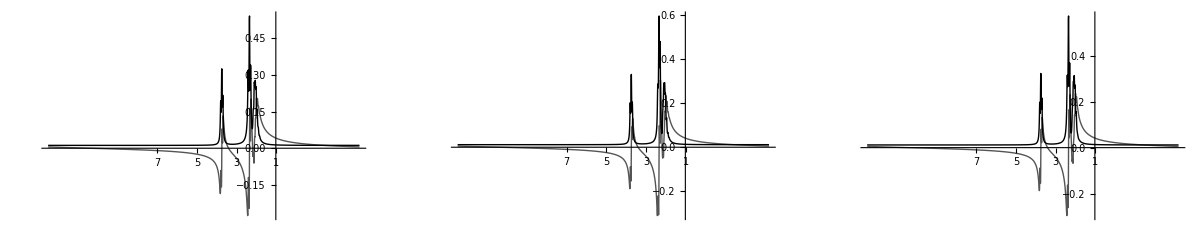

```mathematica
sys=GetSpinSystem["glu"];
{din,struct}=SimHamiltonian[sys];
echoTime=18;

pls=Table[
dout=SequenceSteam[din,struct,{echoTime,tm}/1000];
{time,fids,ppm,spec,dout}=SimReadout[dout,struct,
ReadoutSamples->2048,ReadoutBandwith->2000,Linewidth->5];
pl=PlotSpectrum[ppm,spec,PlotRange->{{1,7},Full}]
,{tm,{6,18,31}(*various mixing times*)}];
GraphicsRow[pls,ImageSize->1200]
```

### Simulate Fat Spectra

#### PulseAcquire

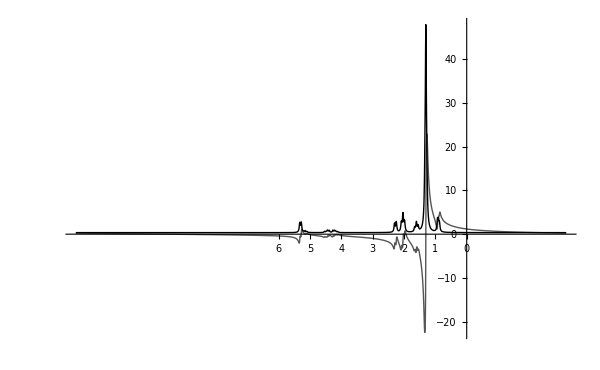

```mathematica
out=Map[(
sys=GetSpinSystem[#];
{din,struct}=SimHamiltonian[sys,FieldStrength->3];
dout=SequencePulseAcquire[din,struct];
SimReadout[dout,struct,
ReadoutSamples->2048,ReadoutBandwith->2000,Linewidth->5]
)&,{"fatGly","fatStart","fatDouble","fatEnd","fatMet"}];
ppm=out[[1,3]];
spec=Total@out[[All,4]];
pl=PlotSpectrum[ppm,spec]
```

#### Spin echo

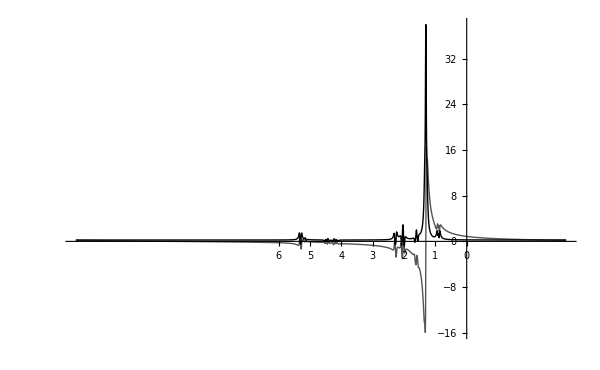

```mathematica
out=(
sys=GetSpinSystem[#];
{din,struct}=SimHamiltonian[sys];
dout=SequenceSpinEcho[din,struct,50/1000];
SimReadout[dout,struct,
ReadoutSamples->2048,ReadoutBandwith->2000,Linewidth->5]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
ppm=out[[1,3]];
spec=Total@out[[All,4]];
pl=PlotSpectrum[ppm,spec]
```

#### STEAM

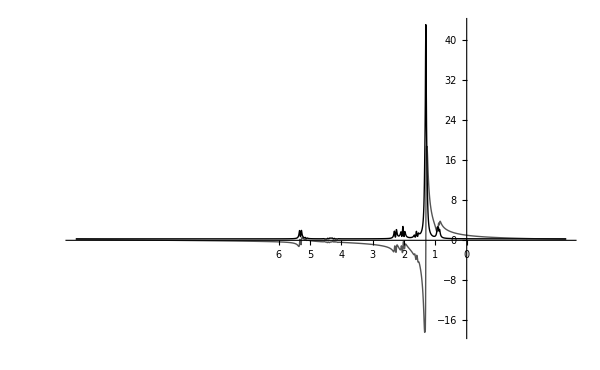

```mathematica
out=(
sys=GetSpinSystem[#];
{din,struct}=SimHamiltonian[sys];
dout=SequenceSteam[din,struct,{50,10}/1000];
SimReadout[dout,struct,
ReadoutSamples->2048,ReadoutBandwith->2000,Linewidth->5]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
ppm=out[[1,3]];
spec=Total@out[[All,4]];
pl=PlotSpectrum[ppm,spec]
```

### Fat STEAM with various TEs

```mathematica
(*simuluate STEAM j coupling for various TEs*)
TEs=Range[10,100,10];
out=(
{din,struct}=SimHamiltonian[#];
ParallelTable[
dout=SequenceSteam[din,struct,{i,16}/1000];
SimReadout[dout,struct,ReadoutSamples->1024,ReadoutBandwith->2000,Linewidth->10]
,{i,TEs}]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
ppm=out[[1,All,3]];
spec=Total[out[[All,All,4]]];
```

```mathematica
(*define the T2 relaxation*)
t2sim=90;
T2relax=Exp[-TEs/t2sim];
max=T2relax[[1]]Max[Abs@spec];
pls=MapThread[PlotSpectrum[#1,#2 #3,PlotRange->{{0,7},{-.5,1}}]&,{ppm,spec/max,T2relax}];
```

```mathematica
Manipulate[pls[[n]],{{n,1,"echo time"},1,Length[pls],1},SaveDefinitions->True]
```